## 第二章 量子力学与线性代数

正交投影算符就是命题

-Graphics-

量子态是希尔伯特空间上迹为1 的正定算符，知道了量子态以后，就能得到该系统的关于任何物理量的任何命题的正确性，进而得到物理量的期望和方差等统计性质

-Graphics-

单比特态的一般形式 -Graphics-

-Graphics-

测量公理给出了经过测量后的瞬间量子系统的状态

-Graphics-

POVM版本的测量公理

应用：非正交的态是不可区分的

每个物理量(可观测量)都与一个PVM对应，用Hermite算符表示物理量

-Graphics-

薛定谔方程与幺正变换。定态是哈密顿量的本征态，不随时间演化。

-Graphics-

复合量子系统的希尔伯特空间是子系统的希尔伯特空间的直积

-Graphics-

态的约化：约化密度矩阵的计算方法

-Graphics-

态的纯化

施密特分解(奇异值分解的应用)

张量积与克罗内克积

线性映射和矩阵的对应关系 -Graphics-

常见的算符和相关性质

正交投影算符

正规变换和Hermite算符

幺正变换

常见的单比特逻辑门的外积形式和矩阵形式：泡利矩阵等

奇异值分解的公式和性质

A = UDV^†

-Graphics-

纠缠体现了复合量子系统的奇妙的关联性，Bell test 展现了Bell态的纠缠性，确认了量子力学的正确性，否定了局域实在论。

## 第四章 量子线路

单比特门U(2)都可以视为qubit生活的空间的旋转，旋转可以一次实现，也可以通过欧拉角分三次实现。

两比特的CU门的制作方法

-Graphics-

测量

隐含测量原理

推迟测量原理

对算符 U 的测量

通用门

定义

H, T, CNOT构成一组通用门

一般的量子门 U(2^n) 不能高效实现

量子计算机的核心要素：初始化、幺正变换、测量

存在一些量子线路以外的量子计算模型

Trotter分解公式，BCH公式与量子模拟

## 第五章 量子算法：量子傅里叶变换及其应用

Deutsch-Jozsa算法展现了量子计算的并行性。

量子傅里叶变换

-Graphics-

bracket算符形式和矩阵形式
-Graphics-
-Graphics--Graphics-

可以用单比特门和两比特门实现QFT， 比特数大约需要  个门

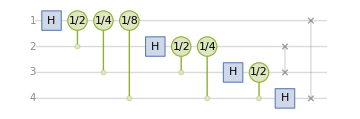

```mathematica
qft4=QuantumCircuitOperator[{"Fourier",4}];
%["Diagram"](*最后交换高低位约定，4比特，12个门*)
```

相位估计：如果能够制备U的本征态，QFT可以用于估计U的本征值。

线路

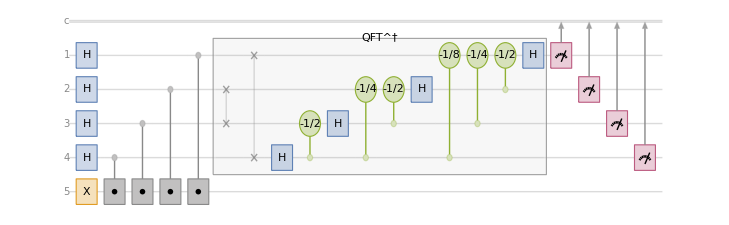

```mathematica
pe1=QuantumCircuitOperator[{"H"->1,"H"->2,"H"->3,"H"->4,"X"->5,Sequence@@Table[QuantumOperator[{"Controlled",QuantumOperator[MatrixPower[u["Matrix"],2^(k-1)],"Label"->label[2^(k-1)]]}]->{5-k,5},{k,1,4}],QuantumCircuitOperator[{"InverseFourier",4}],{1},{2},{3},{4}}];
%//TraditionalForm
```

Shor算法

大数分解的困难性保证了 RSA (Rivest-Shamir-Adleman) 公钥密码通信的安全性5。

Shor算法高效的解决了大数分解问题。

关键步骤：用量子算法求  的周期

-Graphics-

隐藏子群问题